Sampling

### Logistic Function

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
```

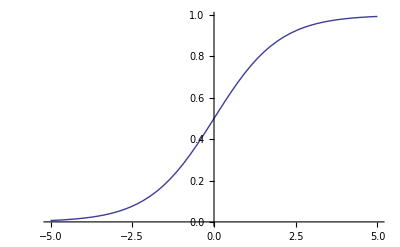

```mathematica
Plot[Logistic[x],{x,-5,5}]
```

### Main Functions

```mathematica
Weight[m_,n_]:=RandomReal[{-1,1},{m,n}]
Visibles[m_]:=RandomInteger[1,m]
Hiddens[n_]:=RandomInteger[1,n]
BiasHiddenSampling[n_]:=RandomInteger[0,n]
BiasVisibleSampling[m_]:=RandomInteger[0,m]
```

### Declarations

```mathematica
RandomSeed[1]
W=Weight[4,5]
V=Visibles[4]
H=Hiddens[5]
BH=BiasHiddenSampling[5]
BV=BiasVisibleSampling[4]
```

RandomSeed[1]

{{-0.219412,0.213563,-0.123808,-0.368196,-0.484718},{-0.341541,0.139236,-0.620891,0.74404,0.51563},{-0.970311,-0.495202,0.0455759,0.102876,0.600469},{0.640959,0.788699,0.713861,-0.868456,0.575624}}

{0,1,1,1}

{0,0,1,0,0}

{0,0,0,0,0}

{0,0,0,0}

```mathematica
dataV=Table[Visibles[4],{i,10}]
```

{{1,0,0,1},{0,1,0,1},{0,1,0,0},{1,0,1,1},{1,1,1,0},{1,0,1,0},{0,1,1,1},{0,1,0,1},{0,1,0,0},{0,0,0,1}}

```mathematica
V2=Visibles[4]
```

{1,0,1,0}

```mathematica
V3=Visibles[4]
```

{0,0,0,0}

### Sampling Functions

```mathematica
sample[l_]:=Map[RandomVariate[BernoulliDistribution[#]]&,l]
```

```mathematica
SampleHidden[w_,bh_][v_]:=sample[Logistic@(wᵀ.v+bh)]
SampleVisible[w_,bv_][h_]:=sample[Logistic@(w.h+bv)]
```

```mathematica
Mean[Table[N @ SampleHidden[W,0*BH ][V],{1000}]]
SampleVisible[W,BV][H]
```

{0.336,0.59,0.522,0.492,0.839}

{1,1,1,1}

```mathematica
W1=Weight[4,5]
```

{{-0.571793,-0.288723,0.928686,0.308795,0.468072},{0.450696,-0.605276,0.300727,-0.767229,-0.98279},{-0.484121,-0.189034,-0.200429,-0.362719,0.168117},{-0.759685,0.307014,-0.0368698,-0.864111,0.297861}}

```mathematica
W2=Weight[4,5]
```

{{0.0526673,0.202912,0.933782,-0.232647,0.0119456},{-0.751207,-0.82033,0.314438,0.298074,-0.197246},{0.22064,-0.616921,-0.429878,-0.31569,0.879237},{-0.334777,0.46148,0.591179,-0.123618,-0.495661}}

```mathematica
W3=W3+0.1*(W1+W2)
```

{{-0.103825,-0.017162,0.372494,0.0152296,0.0960034},{-0.0601023,-0.285121,0.123033,-0.0938311,-0.236007},{-0.0526963,-0.161191,-0.126061,-0.135682,0.209471},{-0.218892,0.153699,0.110862,-0.197546,-0.0395599}}

## Learning

```mathematica
DeltaWeight[bh_,bv_,ϵ_,v1_][w_]:=Module[{h1,v2,h2,w0,w1,wnew},
h1=SampleHidden[w,bh][v1];
v2=SampleVisible[w,bv][h1];
h2=SampleHidden[w,bh][v2];
w0=Outer[Times,v1,h1];
w1=Outer[Times,v2,h2];
wnew=w+ϵ*(w0-w1);
wnew
]
```

```mathematica
SingleLearning[w_,bh_,bv_,ϵ_,n_,v1_]:=Nest[DeltaWeight[bh,bv,ϵ,v1],w,n]
```

```mathematica
SingleLearning[W,BH,BV,0.01,6,V]
```

{{-0.229412,0.203563,-0.123808,-0.378196,-0.484718},{-0.341541,0.159236,-0.590891,0.74404,0.55563},{-0.970311,-0.485202,0.0455759,0.122876,0.620469},{0.640959,0.798699,0.723861,-0.868456,0.595624}}

```mathematica
DataLearning[w_,datalist_,bh_,bv_,ϵ_,n_]:=Fold[SingleLearning[#1,bh,bv,ϵ,n,#2]&,w,datalist]
```

```mathematica
DataLearning[W,dataV,BH,BV,0.01,10]
```

{{-0.179412,0.183563,-0.0838082,-0.358196,-0.544718},{-0.311541,0.109236,-0.800891,0.87404,0.60563},{-1.00031,-0.575202,-0.0544241,0.142876,0.510469},{0.660959,0.728699,0.623861,-0.818456,0.425624}}

## Testing